```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;(* parents directory could be "../LLR/FunctionsAndConstants.wl" etc*)
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
flim=Import["cannex_sensitivity_curves.csv"][[1;;]];
PressSen=Interpolation[flim[[All,1;;2]]]; (*Function of d in meters, output in N/m^2*)
PressGradSen=Interpolation[flim[[All,1;;3;;2]]]; (*Function of d in meters, output in N/m^3*)
```

Import::nffil: File cannex_sensitivity_curves.csv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

## Pressure limits

## Compare simulation to analytically exact solution as well as pressure - ok!

```mathematica
ρeff[M_,μ_,ρM_]:=ρM-M^2 μ^2
μeff[M_,μ_,ρV_]:=√(μ^2-ρV/M^2)
EQN[M_,μ_,ρV_,ρM_,k_,d_]:=√(1-k^2/2)-√(1+ρeff[M,μ,ρM]/(M^2*μeff[M,μ,ρV]^2))*Abs[JacobiCD[μeff[M,μ,ρV]*√(1-k^2/2)*d,((Abs[k]/√2)/(√(1-k^2/2)))^2]]
ϕ1[z_,μ_,λ_, M_,ρV_,k_]:=ϕρ[μ,λ, M,ρV]*k*JacobiCD[μeff[M,μ,ρV]*√(1-k^2/2)*z,((Abs[k]/√2)/(√(1-k^2/2)))^2]
ϕ2[z_,μ_,λ_, M_,ρM_,k_,ϕd_,d_]:=√((2*ρeff[M,μ,ρM])/λ)*1/M*1/Sinh[(√ρeff[M,μ,ρM])/M(Abs[z]-d)+ArcSinh[√((2*ρeff[M,μ,ρM])/λ)*1/(M*ϕd)]]
ϕFull[z_,μ_,λ_, M_,ρV_,ρM_,k_,ϕd_,d_]:=Piecewise[{{ϕ2[z,μ,λ, M,ρM,k,ϕd,d],Abs[z]>d}},ϕ1[z,μ,λ, M,ρV,k]]
```

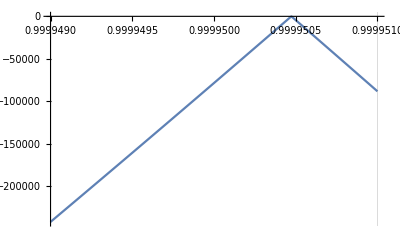

```mathematica
μ=SetPrecision[10^-0.5*10^-6,30];
M=SetPrecision[10^-6.2*10^3,30];
λ=10^3;
Plot[EQN[M,μ,ρV,ρM,k,dd*m2invMeV/2],{k,0.999949,0.999951},PlotRange->Full,GridLines->{{k}}]
```

```mathematica
k=SetPrecision[0.9999504732,1000];
ϕd=ϕ1[-dd*m2invMeV/2,μ,λ, M,ρV,k];
EQN[M,μ,ρV,ρM,k,dd*m2invMeV/2]
```

-4.786125556567018649471

-4.786125556567018649471

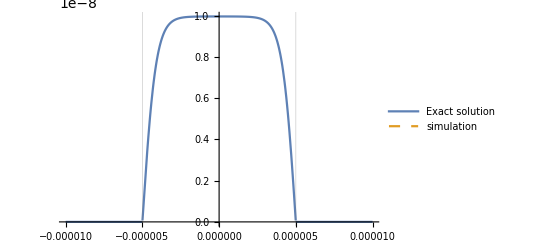

```mathematica
(*μ=SetPrecision[10^-1*10^-6,30];
M=SetPrecision[1*10^3,30];
λ=10^-5;*)
k=SetPrecision[0.9999504732,1000];
ϕd=ϕ1[-dd*m2invMeV/2,μ,λ, M,ρV,k];
EQN[M,μ,ρV,ρM,k,dd*m2invMeV/2]
Prec=15;
MAX=100;
Sol=SOLVEFD[μ,M,λ,a,points,Prec,MAX,dd][[2]];

SOL[z_]:=ϕFull[z*m2invMeV,μ,λ, M,ρV,ρM,k,ϕd,dd*m2invMeV/2]

Plot[{SOL[z],Sol[z]},{z,-dd,dd},GridLines->{{-dd/2,dd/2}},PlotRange->Full,PlotStyle-> {Thick,Dashed},PlotLegends->{"Exact solution","simulation"}]
```